## Read data in

```mathematica
SetDirectory["ADD PATH TO FILES HERE"];
files=FileNames["Evo_N1000_M500_mu0.000_nuL_0.010_nuR_0.010_nur0.010_rGlob0.50_kon1.00_koff1.00_f1.00_g0.50_K*_n1.0_sigma0.10_dv00.00_time*_1_rep17.txt"]
files= files[[Ordering@PadRight@StringSplit[files,x:DigitCharacter..:>FromDigits@x]]];
sEvo=Flatten[Table[ReadList[files[[f]],Number],{f,1,Length[files]}]//N];

files=FileNames["Evo_N1000_M500_mu0.000_nuL_0.010_nuR_0.010_nur0.010_rGlob0.50_kon1.00_koff1.00_f1.00_g0.50_K*_n1.0_sigma0.10_dv00.00_time*_2_rep17.txt"]
files= files[[Ordering@PadRight@StringSplit[files,x:DigitCharacter..:>FromDigits@x]]];
rEvo=Flatten[Table[ReadList[files[[f]],Number],{f,1,Length[files]}]//N];
```

{Evo_N1000_M500_mu0.000_nuL_0.010_nuR_0.010_nur0.010_rGlob0.50_kon1.00_koff1.00_f1.00_g0.50_K0.9_n1.0_sigma0.10_dv00.00_time100000_1_rep17.txt}

{Evo_N1000_M500_mu0.000_nuL_0.010_nuR_0.010_nur0.010_rGlob0.50_kon1.00_koff1.00_f1.00_g0.50_K0.9_n1.0_sigma0.10_dv00.00_time100000_2_rep17.txt}

```mathematica
rEvo=Flatten[rEvo];
sEvo=Flatten[sEvo];
```

```mathematica
(*Thin out data*)
rEvoShort = Table[{i, rEvo[[i]]}, {i,1,Length[rEvo]/10,1}];
sEvoShort = Table[{i, sEvo[[i]]}, {i,1,Length[sEvo]/10,1}];
rsEvoShort = Table[{rEvo[[i]], sEvo[[i]]}, {i,1,2000,1}];
```

## Evolution over time

```mathematica
(*get average by multiplying by frequency*)
```

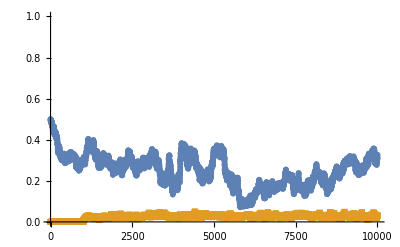

```mathematica
Show[ListPlot[{rEvoShort,sEvoShort}, Joined->True, PlotRange->{{0,10000},{0,1}},PlotStyle->Thick, PlotMarkers->{Automatic,6},AxesStyle->Thickness[0.0015]], Axis->Thick,TicksStyle->Directive[16, Black, FontFamily->"Times"]]
```